# Análisis

## De los umbrales de tiempo (relación cantidad de personas, cantidad unidades de tiempo) en combinación con diferentes capcidades

People=10,50,100,500,1000
Time=100,100,1000,1000,10000
Capacity=2,4,6,8,10

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Valores:

exTimes es la cantidad de ejecuciones que se realizaron, las carpetas con los grafos debén estar nombradas con los números desde el 1 hasta exTimes

```mathematica
capacity=Range[2,10,2];
peopleVals={10,50,100,500,1000};
timeVals={100,250,1000,5000,10000};
avClustering={};
avApl={};
sDClustering={};
sDApl={};
exTimes=2;
```

## Función para importar los grafos

Se importan los grafos de todas las ejecuciones para una configuracion de personas - capacidad
people y time serán tratados como listas de x y y de las parejas correspondientes, es decir {x1,y1},{x2,y2}, etc.

```mathematica
ImportGraphs[i_,j_]:=
Table[Import[StringJoin["graphs/model-v3/",IntegerString[exNumber],"/","network-",IntegerString[peopleVals[[i]]],"-",IntegerString[capacity[[j]]],"-",IntegerString[timeVals[[i]]],".g6"]],{exNumber,1,exTimes,1}];
```

## Función para calcular el promedio y la desviación estándar del clustering coefficient y del average path length

```mathematica
CalulateVals[i_,j_]:=Module[{listClustering,meanClustering,sdClustering,listApl,meanApl,sdApl},
networks=ImportGraphs[i,j];

listClustering=Map[GlobalClusteringCoefficient,networks];
meanClustering=Mean[listClustering];
sdClustering=StandardDeviation[listClustering];

listApl=Map[MeanGraphDistance,networks];
meanApl=Mean[listApl];
sdApl=StandardDeviation[listApl];

avClustering=Append[avClustering,meanClustering];
sDClustering=Append[sDClustering,sdClustering];
avApl=Append[avApl,meanApl];
sDApl=Append[sDApl,sdApl];
];
```

## Función para calcular todas las configuraciones personas - capacidad

```mathematica
AverageVals:=Module[{},
Do[CalulateVals[i,j],{i,1,Length[peopleVals],1},{j,1,Length[capacity],1}];
];
```

## Graficas

```mathematica
AverageVals;
```

Infinity::indet: Indeterminate expression -∞ + ∞ encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

### Clustering coefficient

```mathematica
avClustering=Partition[avClustering,5];
```

#### capacity vs clustering coefficient

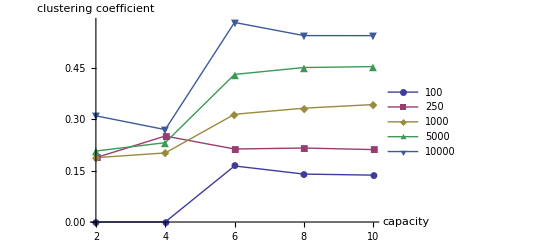

```mathematica
dataPlotCl1=Table[Table[{capacity[[k]],avClustering[[k,t]]},{k,1,Length[capacity],1}],{t,1,Length[timeVals],1}];
ListLinePlot[dataPlotCl1,PlotLegends->timeVals,AxesLabel->{"capacity","clustering coefficient"},PlotMarkers->Automatic]
```

#### time vs clustering coefficient

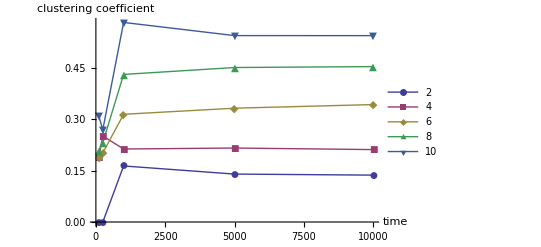

```mathematica
dataPlotCl2=Table[Table[{timeVals[[t]],avClustering[[t,k]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
ListLinePlot[dataPlotCl2,PlotLegends->capacity,AxesLabel->{"time","clustering coefficient"},PlotMarkers->Automatic]
```

#### people vs clustering coefficient

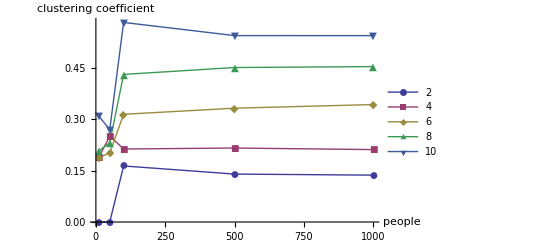

```mathematica
data=Table[{peopleVals[[x]],capacity[[y]]},{x,1,Length[peopleVals],1},{y,1,Length[capacity],1}];
(*dataPlotCl3=Table[Append[Flatten[data,1][[z]],Flatten[avClustering,1][[z]]],{z,1,Length[Flatten[avClustering,1]],1}];*)
dataPlotCl3=Table[Table[{peopleVals[[t]],avClustering[[t,k]]},{t,1,Length[peopleVals],1}],{k,1,Length[capacity],1}];
ListLinePlot[dataPlotCl3,PlotLegends->capacity,AxesLabel->{"people","clustering coefficient"},PlotMarkers->Automatic]
(*ListPlot[dataPlotCl3]*)
```

```mathematica
N[Mean[Flatten[Table[avClustering[[t]],{t,1,3,1}]]]]
N[Mean[Flatten[Table[avClustering[[t]],{t,4,Length[avClustering],1}]]]]
```

0.236346

0.264675

```mathematica
dataPlot1=Table[Table[{peopleVals[[t]],avClustering[[t,k]]},{t,1,3,1}],{k,1,Length[capacity],1}];
dataPlot2=Table[Table[{peopleVals[[t]],avClustering[[t,k]]},{t,3,Length[capacity],1}],{k,1,Length[capacity],1}];
```

```mathematica
(*dataPlot2=Table[Table[{timeVals[[p]],Flatten[avClustering][[p+k-1]]},{p,1,Length[peopleVals],1}],{k,1,Length[capacity],1}]*)
```

{{{100,0},{100,5/64},{1000,11479/51072},{1000,134413/417600},{10000,26774227/50642592}},{{100,5/64},{100,11479/51072},{1000,134413/417600},{1000,26774227/50642592},{10000,0}},{{100,11479/51072},{100,134413/417600},{1000,26774227/50642592},{1000,0},{10000,0}},{{100,134413/417600},{100,26774227/50642592},{1000,0},{1000,0},{10000,1/32}},{{100,26774227/50642592},{100,0},{1000,0},{1000,1/32},{10000,474023/3610880}}}

### Average path length

```mathematica
avApl=Partition[avApl,5];
```

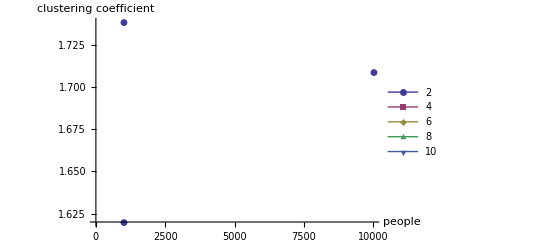

```mathematica
dataPlotApl=Table[Table[{timeVals[[t]],avApl[[t,k]]},{t,1,Length[timeVals],1}],{k,1,Length[capacity],1}];
ListLinePlot[dataPlotApl,PlotLegends->capacity,AxesLabel->{"people","clustering coefficient"},PlotMarkers->Automatic]
```

```mathematica
ListLinePlot
```